```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Documents and Settings\Rob Sheehan\My Documents\Dropbox\PhD_Thesis\Scattering_Matrix_Analysis_Optical_Waveguides

## Modules

### Reflection and Transmission Coefficients

```mathematica
(* Critical Angle *)
thcrit[n1_,n2_]:=ArcSin[n2/n1];
```

```mathematica
(* Phase change due to propagation of distance d *)
dphase[n_,d_,θ_,λ_]:=N[(2π)/λ n d Cos[θ]];
```

```mathematica
(* Propagation angle in medium 2 after passing through medium 1 from Snell's law *)
θnew[n1_,n2_,θ1_]:=N[ArcSin[n1/n2 Sin[θ1]]];
```

```mathematica
(* reflection coefficient at an interface *)
refl[n1_,n2_,θ1_,pol_]:=Module[
{numer,denom,indxrat,t1,t2,θ2},
(* reflection coefficient at an interface *)
(* R. Sheehan 8 - 4 - 2013 *)

indxrat =N[n2/n1]; (* refractive index ratio *)
θ2=θnew[n1,n2,θ1]; (* θ2 = ArcSin(Sin(θ1)/n) *)
t1=N[Cos[θ1]]; 
t2=N[indxrat Cos[θ2]]; 
numer=N[t1-t2];(* Cos(θ1) - n Cos(θ2) *)
denom=N[t1+t2]; (* Cos(θ1) + n Cos(θ2) *) 
Return[N[numer/denom]]; 
]
```

```mathematica
(* transmission coefficient at an interface *)

tran[n1_,n2_,θ1_,pol_]:=Module[
{numer,denom,indxrat,t1,t2,θ2},
(* transmission coefficient at an interface *)
(* R. Sheehan 8 - 4 - 2013 *)

indxrat = N[n2/n1]; (* refractive index ratio *)
θ2=N[ArcSin[1.0/indxrat Sin[θ1]]]; 
t1=N[Cos[θ1]]; 
t2=N[indxrat Cos[θ2]]; 
numer=N[2.0t1];(* 2 Cos(θ1) *)
denom=N[t1+t2]; (* Cos(θ1) + n Cos(θ2) *) 
Return[N[numer/denom]]; 
]
```

```mathematica
tranrefl[n1_,n2_,θ1_,pol_]:=Module[
{numer,denom,indxrat,t1,t2,θ2,refl,tran},
(* Compute the transmission and reflection coefficients at an  *)
(* interface between two dielectrics, assuming an input angle of Subscript[θ, 1] *)
(* R. Sheehan 8 - 4 - 2013 *)

indxrat = n2/n1; (* refractive index ratio *)
θ2=θnew[n1,n2,θ1](*ArcSin[1.0/indxrat Sin[θ1]]*); (* Compute the output angle according to Snell's law *)
t1=Cos[θ1]; 
t2=indxrat Cos[θ2]; 
numer=t1-t2;
denom=t1+t2; 
refl=N[numer/denom]; (* Cos(θ1) - n Cos(θ2) / Cos(θ1) + n Cos(θ2) *)
tran=N[(2.0t1)/denom]; (* 2 Cos(θ1) / Cos(θ1) + n Cos(θ2) *)
Return[{θ2,refl,tran}]
]
```

### Scattering matrix for an interface

```mathematica
Smatrix[n1_,n2_,d_,θ1_,pol_,λ_]:=Module[
{dval,θ2,rval,tval,t1,t2,S,s11,s12,s21,s22},
(* Compute the scattering matrix for a single dielectric layer *)
(* R. Sheehan 8 - 4 - 2013 *)

dval=dphase[n1,d,θ1,λ]; (* Phase change due to propagation through distance d at angle θ1 *)

{θ2,rval,tval}=tranrefl[n1,n2,θ1,pol]; (* Compute refl. trans. coefficients due to layer *)

t1=N[1.0/tval]; t2=N[rval/tval];

s11=t1 ⅇ^(ⅈ dval); 
s12= t2 ⅇ^(ⅈ dval); 
s21= t2 ⅇ^(-ⅈ dval); 
s22=t1 ⅇ^(-ⅈ dval);

S=({{s11, s12}, {s21, s22}}); 

Return[{θ2,S}]; 
]
```

### Multi-layer analysis

```mathematica
ScatteringMatrixAnalysis[Nt_,λ_,pol_,indxlist_]:=Module[
{data,θu=N[π/2.0],θl=N[ArcSin[indxlist⟦2,2⟧/indxlist⟦1,2⟧]],θ,θlast,θnext,S,Slayer,dt},
(* Perform a scattering matrix analysis of an optical structure described by indxlist *)
(* R. Sheehan 28 - 4 - 2013 *)

dt=N[(θu-θl)/(Nt-1)];(* Compute the angular spacing *)

data=Table[0,{0}]; (* Initialise the array to hold the scattering data *)

θ=θl; (* Initialise the calculation *)
Do[
(* Step through the structure at the given angle *)

(* Initialise the input angle *)
θlast=θ; 

Do[

(* Compute the scattering matrix for each layer in the structure *)
{θnext,Slayer}=Smatrix[indxlist⟦i,2⟧,indxlist⟦i+1,2⟧,indxlist⟦i,1⟧,θlast,pol,λ];

(* Compute the scattering matrix for the structure *)
Which[
i==1,S=Slayer,
i>1,S=S.Slayer;
];

(* Update the angle of propagation *)
θlast=θnext;

 ,{i,1,Length[indxlist]-1}];

AppendTo[data,{indxlist⟦1,2⟧ Sin[θ],S⟦1,1⟧,S⟦1,2⟧,S⟦2,1⟧,S⟦2,2⟧}];

θ=θ+dt; 

,{t,1,Nt}];

Return[data]; 
]
```

### Data Analysis

```mathematica
(* Lorentzian Peak Fit *)

LorentzFit[data_,aest_,best_,gest_]:=Module[
{thefit,fitparams,theplot,resplot,model,a,g,x,b,nparams = 3,ν,peakval},
(* Fit a Lorentzian function to a data set *)
(* Return the fit and some statistics *)
(* R. Sheehan 25 - 4 - 2013 *)

ν = Length[data]-nparams-1; 

model=(a g)/((x-b)^2+g^2); 

thefit=NonlinearModelFit[data,model,{{a,aest},{b,best},{g,gest}},x];

fitparams=thefit["BestFitParameters"]; 

peakval=fitparams⟦1,-1⟧/fitparams⟦3,-1⟧; 

Print["The peak is located at ",fitparams⟦2,-1⟧];
Print["The full-width at half-max is ",fitparams⟦3,-1⟧];
Print["The peak value is ",N[peakval]];
(* Quality of fit *)
(* In general you want R^2 = 1 and Subscript[(χ^2), ν] = 1, assuming errors are normally distributed *)
Print["The R^2 parameter for the fit is ",thefit["RSquared"]];
Print["The Adjusted R^2 parameter for the fit is ",thefit["AdjustedRSquared"]];
(*Print["The χ^2 parameter for the fit is ",thefit["AIC"]-2.0nparams," or ",thefit["BIC"]-nparams Log[Length[data]]];
Print["The reduced χ^2 parameter for the fit is ",(thefit["AIC"]-2.0nparams)/ν," or ",(thefit["BIC"]-nparams Log[Length[data]])/ν];*)

theplot=Plot[Normal[thefit],{x,First[data]⟦1⟧,Last[data]⟦1⟧},PlotRange->{All,Automatic},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Blue}},AxesLabel->{"n_eff",None},PlotLabel->Style["The Fit R^2 = "<>ToString[thefit["RSquared"]],Bold,18],
Epilog->{
{Darker[Green],Point[data]},
Dashed,Red,
Line[{{fitparams⟦2,-1⟧,0},{fitparams⟦2,-1⟧,peakval}}],Line[{{fitparams⟦2,-1⟧-fitparams⟦3,-1⟧,0.5peakval},{fitparams⟦2,-1⟧+fitparams⟦3,-1⟧,0.5peakval}}]}
];

resplot=ListPlot[
Table[{data⟦i,1⟧,thefit["FitResiduals"]⟦i⟧},{i,1,Length[data]}],
PlotRange->{All,All},AxesStyle->Thick,LabelStyle->{Bold,18},AxesLabel->{"n_eff",None},PlotLabel->Style["Fit Residuals",Bold,18],
Filling->Axis];

Return[{thefit,theplot,resplot}]
]
```

```mathematica
NotebookSave[]
```

## Module Testing

### Plots for a single angle

```mathematica
ntest[x_]:=Piecewise[{{1.5, x<0.0}, {1.4, 0≤x≤0.6}, {1.5, 0.6≤x≤(0.6+2.0)}}]
```

```mathematica
ntestcor[x_]:=Piecewise[{{1.5, 0.6≤x≤(0.6+2.0)}, {1.4, True}}]
```

```mathematica
n[x_]:=Piecewise[{{1.503, Abs[x]≤2.0}, {1.5, Abs[x]>2.0}}];
λ=1.55;
```

```mathematica
xtcks={{0,"0"},{0.6,"d_2"},{2.6,"d_2+d_3"}};
ytcks={{1.4,"n_2"},{1.5,"n_1"}};
```

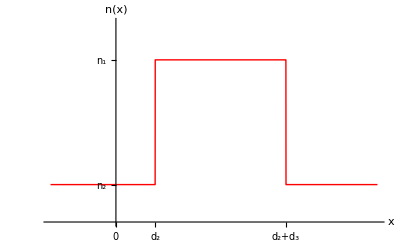

```mathematica
indxplt=Plot[{ntestcor[x]},{x,-1,4},PlotRange->{All,{1.37,1.53}},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{Thick,Red},AxesLabel->{"x","n(x)"},Exclusions->None,Ticks->{xtcks,ytcks}]
```

```mathematica
(*Export["Indx_Pic.pdf",indxplt]*)
```

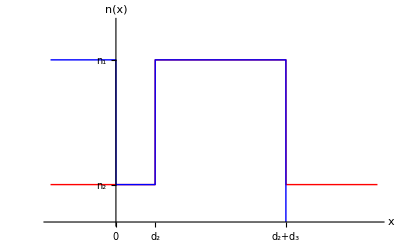

```mathematica
Plot[{ntestcor[x],ntest[x]},{x,-1,4},PlotRange->{All,{1.37,1.53}},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Red},{Thick,Blue}},AxesLabel->{"x","n(x)"},Exclusions->None,Ticks->{xtcks,ytcks}]
```

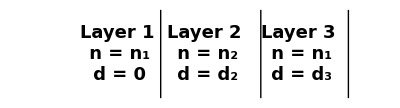

```mathematica
pic2=Graphics[{
{Thick,Line[{{0,0},{0,1}}],Line[{{1.6,0},{1.6,1}}],Line[{{3,0},{3,1}}]},
Text[Style["Layer 1\n n = n_1\n d = 0",Bold,18],{-0.7,0.5}],
Text[Style["Layer 2\n n = n_2\n d = d_2",Bold,18],{0.7,0.5}],
Text[Style["Layer 3\n n = n_1\n d = d_3",Bold,18],{2.2,0.5}]
}]
```

```mathematica
(*Export["Equiv_Pic.pdf",pic2]*)
```

```mathematica
λ=1.0; 
n1=1.5;
n2=1.4;
width=2.0; 
d2=0.3; 
tu=N[π/2]; 
tl=N[ArcSin[n2/n1]];
Print["Critical Angle  = ",tl]
```

Critical Angle  = 1.20359

```mathematica
θ=tl+(tu-tl)/2
```

1.38719

```mathematica
{θ2,S1}=Smatrix[n1,n2,0.0,θ,True,λ];
{θ,r1,t1}=tranrefl[n1,n2,θ,True];
δ=dphase[n2,0.0,θ,λ];
Print["θ2 = ",θ2,", t = ",t1,", r = ",r1,", δ = ",δ,", S1 = ",MatrixForm[S1]]

{θ3,S2}=Smatrix[n2,n1,d2,θ2,True,λ];
{θ,r2,t2}=tranrefl[n1,n2,θ,True];
δ=dphase[n1,d2,θ2,λ];
Print["θ3 = ",θ3,", t = ",t2,", r = ",r2,", δ = ",δ,", S2 = ",MatrixForm[S2]]

{θ4,S3}=Smatrix[n1,n2,width,θ3,True,λ];
{θ,r3,t3}=tranrefl[n1,n2,θ,True];
δ=dphase[n2,width,θ3,λ];
Print["θ4 = ",θ4,", t = ",t3,", r = ",r3,", δ = ",δ,", S3 = ",MatrixForm[S3]]

S=(S1.S2); 
S=(S.S3); 
Print["S = ",MatrixForm[S]]
```

θ2 = 1.5708-0.325426 ⅈ, t = 0.517241-0.875753 ⅈ, r = -0.482759-0.875753 ⅈ, δ = 0.+0. ⅈ, S1 = (0.5+0.846562 ⅈ | 0.5-0.846562 ⅈ
0.5-0.846562 ⅈ | 0.5+0.846562 ⅈ)

θ3 = 1.38719-2.22045×10^-16 ⅈ, t = 0.808151-3.01955×10^-17 ⅈ, r = -0.191849-3.01955×10^-17 ⅈ, δ = 1.82379×10^-16+0.936448 ⅈ, S2 = (0.208636-0.123225 ⅈ | 0.208636+0.123225 ⅈ
1.19826+0.707722 ⅈ | 1.19826-0.707722 ⅈ)

θ4 = 1.5708-0.325426 ⅈ, t = 0.90388-1.14732×10^-17 ⅈ, r = -0.0961196-1.14732×10^-17 ⅈ, δ = 3.21201+3.84075×10^-15 ⅈ, S3 = (-0.227636-0.956477 ⅈ | -0.727745+0.661101 ⅈ
-0.227636+0.956477 ⅈ | -0.727745-0.661101 ⅈ)

S = (0.238797-0.964247 ⅈ | -1.41027+2.14948 ⅈ
0.238797+0.964247 ⅈ | -1.41027-2.14948 ⅈ)

```mathematica
tl
```

1.20359

### Multi-angle analysis

```mathematica
λ=1.0; 
n1=1.5;
n2=1.4;
width=2.0; 
d2=0.3; 

tl=N[ArcSin[n2/n1]];
tu=π/2.0; 
Nt=701; 
dt=(tu-tl)/(Nt-1);
θ=tl; 

data=Table[0,{0}]; 

Do[
{θ2,S1}=Smatrix[n1,n2,0.0,θ,True,λ];
{θ3,S2}=Smatrix[n2,n1,d2,θ2,True,λ];
{θ4,S3}=Smatrix[n1,n2,width,θ3,True,λ];
S=(S1.S2); 
S=(S.S3); 
(*Print[angles⟦t⟧," , ",Abs[1.0/(S⟦1,1⟧)^2]," , ",MatrixForm[S]];*)
AppendTo[data,{n1 Sin[θ],S⟦1,1⟧,S⟦1,2⟧,S⟦2,1⟧,S⟦2,2⟧}];
θ=θ+dt; 
,{t,1,Nt}]
```

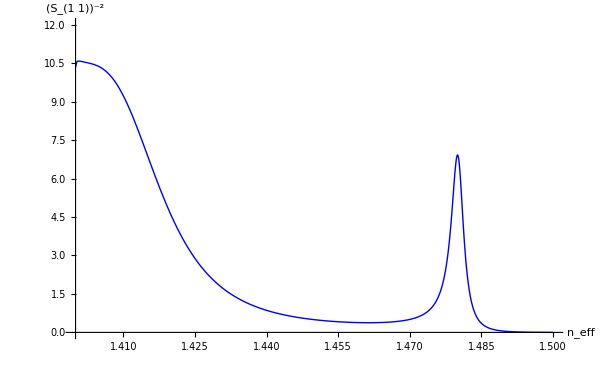

```mathematica
pltdata1=Map[{#1⟦1⟧,Abs[1.0/(#1⟦2⟧)^2]}&,data]; 
plt1=ListPlot[pltdata1,Joined->True,PlotRange->{All,{0,12}},AxesLabel->{"n_eff","(S_(1 1))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{Thick,Blue},ImageSize->{600,360}]
```

```mathematica
(*Export["Full_1.pdf",plt1]*)
```

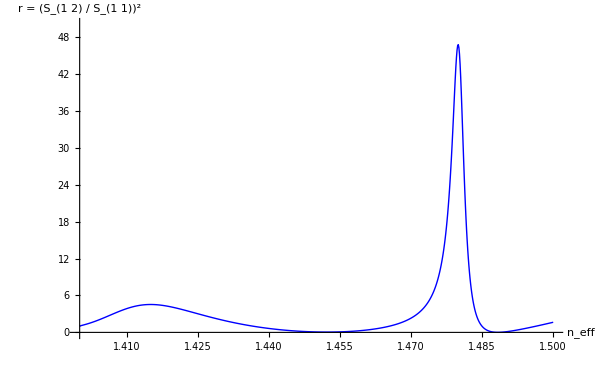

```mathematica
pltdata2=Map[{#1⟦1⟧,Abs[(#1⟦3⟧)^2/(#1⟦2⟧)^2]}&,data];
plt2=ListPlot[pltdata2,Joined->True,PlotRange->{All,{0,50}},AxesLabel->{"n_eff","r = (S_(1 2) / S_(1 1))^2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{Thick,Blue},ImageSize->{600,360}]
```

```mathematica
(*Export["Full_2.pdf",plt2]*)
```

```mathematica
(*Show[plt2,lines]*)
```

```mathematica
(*Export["Sample_Data.txt",pltdata4,"CSV"]*)
```

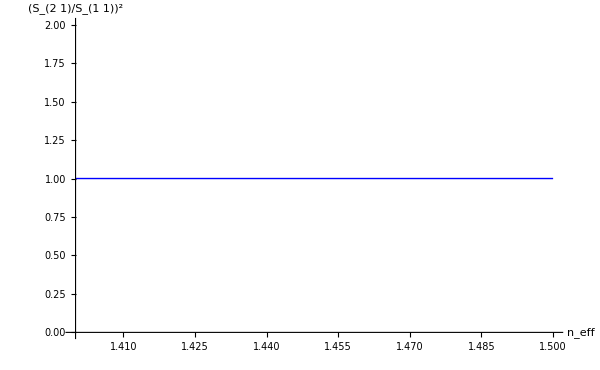

```mathematica
pltdata3=Map[{#1⟦1⟧,Abs[(#1⟦4⟧)^2/(#1⟦2⟧)^2]}&,data];
plt3=ListPlot[pltdata3,Joined->True,PlotRange->{All,{0,2}},AxesLabel->{"n_eff","(S_(2 1)/S_(1 1))^2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{Thick,Blue},ImageSize->{600,360}
]
(*Show[plt3,lines]*)
```

```mathematica
(*Export["Full_3.pdf",plt3]*)
```

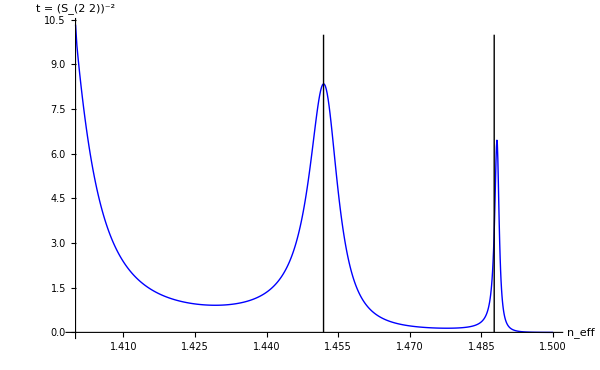

```mathematica
pltdata4=Map[{#1⟦1⟧,Abs[1.0/(#1⟦5⟧)^2]}&,data];
plt4=ListPlot[{pltdata4},Joined->True,PlotRange->{All,All},PlotMarkers->None,AxesLabel->{"n_eff","t = (S_(2 2))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Blue},{Thick,Dashed,Red},Dotted},ImageSize->{600,360},Epilog->{Line[{{1.451928782,0},{1.451928782,+10}}],Line[{{1.487663309,0},{1.487663309,+10}}]}]
```

```mathematica
(*Export["Sample_Data_Plot.pdf",plt4]*)
```

```mathematica
(*Export["Full_4.pdf",plt4]*)
```

```mathematica
NotebookSave[]
```

### Modularised Multi-angle analysis

```mathematica
λ=1.0; 
n1=1.5;
n2=1.4;
width=2.0; 
d2=0.5;
Nt=501;
```

```mathematica
indxlist={{0.0,n1},{d2,n2},{width,n1},{0.0,n2}};
```

```mathematica
data=ScatteringMatrixAnalysis[Nt,λ,True,indxlist];
```

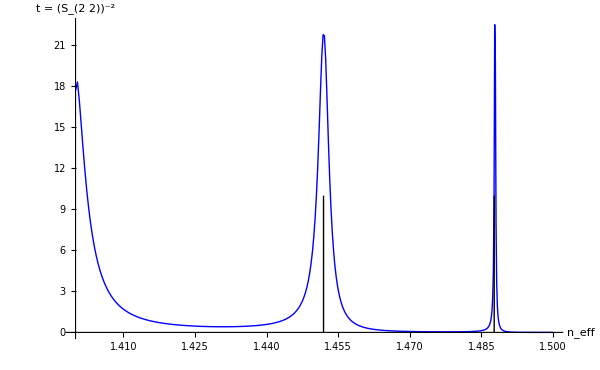

```mathematica
pltdata4=Map[{#1⟦1⟧,Abs[1.0/(#1⟦5⟧)^2]}&,data];
plt4=ListPlot[pltdata4,Joined->True,PlotRange->{All,All},PlotMarkers->None,AxesLabel->{"n_eff","t = (S_(2 2))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Blue},{Thick,Dashed,Red},Dotted},ImageSize->{600,360},Epilog->{Line[{{1.451928782,0},{1.451928782,+10}}],Line[{{1.487663309,0},{1.487663309,+10}}]}]
```

### Fitting to the data

```mathematica
(* Want to fit a lorentzian to the data around the peaks *)
```

```mathematica
xl=1.486; xu=1.49; 
(*xl=1.445; xu=1.46; *)
```

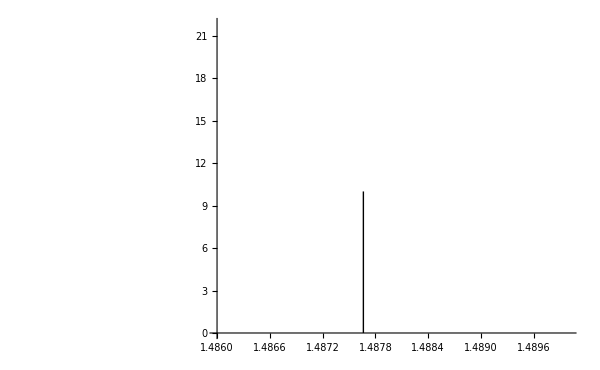

```mathematica
pltdata4=Map[{#1⟦1⟧,Abs[1.0/(#1⟦5⟧)^2]}&,data];
plt4=ListPlot[pltdata4,Joined->False,PlotRange->{{xl,xu},All},PlotMarkers->Automatic,AxesLabel->{"n_eff","t = (S_(2 2))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Blue}},ImageSize->{600,360},Epilog->{Line[{{1.451928782,0},{1.451928782,10}}],Line[{{1.487663309,0},{1.487663309,10}}]}]
```

```mathematica
(*xl=1.486; xu=1.49; *)
(*xl=1.44; xu=1.46; *)
(*datasubset=Table[0,{0}];
Do[
If[pltdata4⟦i,1⟧<xu&&pltdata4⟦i,1⟧>xl,AppendTo[datasubset,pltdata4⟦i⟧] ]
,{i,1,Length[pltdata4]}];*)

datasubset=Select[pltdata4,#1⟦1⟧>xl&&#1⟦1⟧<xu&];
```

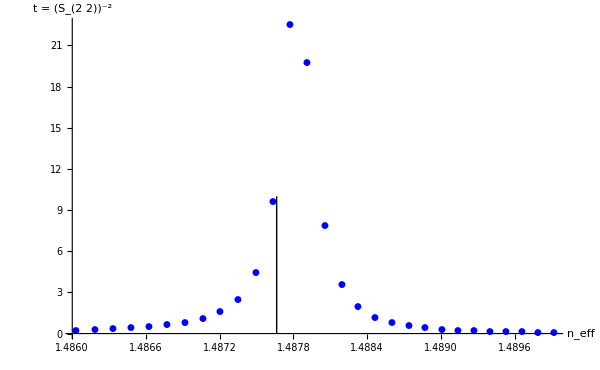

```mathematica
ListPlot[datasubset,Joined->False,PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"n_eff","t = (S_(2 2))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Blue},{Thick,Dashed,Red},Dotted},ImageSize->{600,360},Epilog->{Line[{{1.451928782,0},{1.451928782,10}}],Line[{{1.487663309,0},{1.487663309,10}}]}]
```

```mathematica
aa=6.0;
bb=1.488; 
gg=1×10^-3;
thefit=LorentzFit[datasubset,aa,bb,gg];
```

The peak is located at 1.48783

The full-width at half-max is 0.000150769

The peak value is 25.7376

The R^2 parameter for the fit is 0.999572

The Adjusted R^2 parameter for the fit is 0.999523

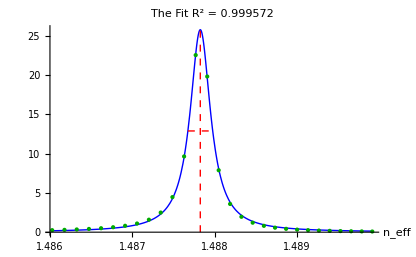

```mathematica
thefit⟦2⟧
```

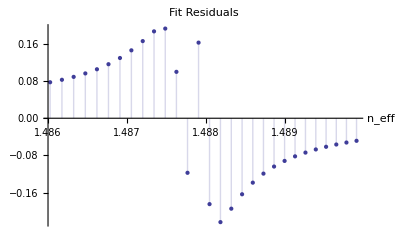

```mathematica
thefit⟦3⟧
```

```mathematica
NotebookSave[]
```

## Examples

### Example 0

```mathematica
λ=1.0;
n1=1.5;
n2=1.4;
width=2.0; 
d2=1.0;
Nt=501; 
indxlist={{0.0,n1},{d2,n2},{width,n1},{0.0,n2}};
```

```mathematica
data=ScatteringMatrixAnalysis[Nt,λ,True,indxlist];
```

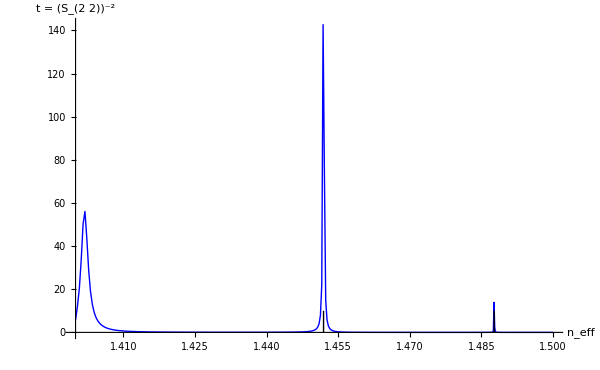

```mathematica
pltdata4=Map[{#1⟦1⟧,Abs[1.0/(#1⟦5⟧)^2]}&,data];
plt4=ListPlot[pltdata4,Joined->True,PlotRange->{All,All},PlotMarkers->None,AxesLabel->{"n_eff","t = (S_(2 2))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Blue},{Thick,Dashed,Red},Dotted},ImageSize->{600,360},Epilog->{Line[{{1.451928782,0},{1.451928782,+10}}],Line[{{1.487663309,0},{1.487663309,+10}}]}]
```

```mathematica
xl=1.485;xu=1.49;
datasubset=Select[pltdata4,#1⟦1⟧>xl&&#1⟦1⟧<xu&];
```

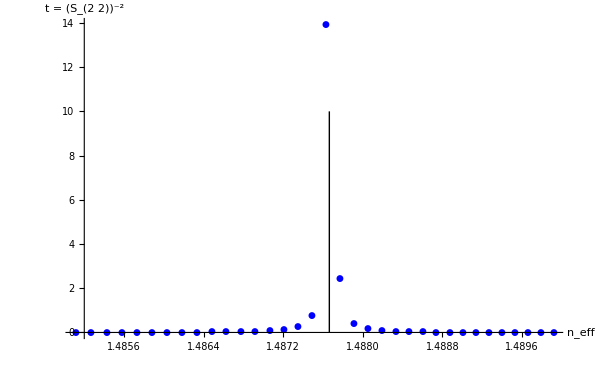

```mathematica
ListPlot[datasubset,Joined->False,PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"n_eff","t = (S_(2 2))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Blue},{Thick,Dashed,Red},Dotted},ImageSize->{600,360},Epilog->{Line[{{1.451928782,0},{1.451928782,10}}],Line[{{1.487663309,0},{1.487663309,10}}]}]
```

```mathematica
aa=6.0;
bb=1.488; 
gg=1×10^-3;
thefit=LorentzFit[datasubset,aa,bb,gg];
```

The peak is located at 1.48767

The full-width at half-max is 0.0000134995

The peak value is 138.023

The R^2 parameter for the fit is 0.999991

The Adjusted R^2 parameter for the fit is 0.99999

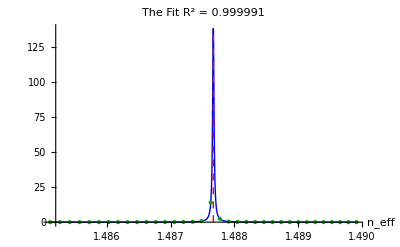

```mathematica
thefit⟦2⟧
```

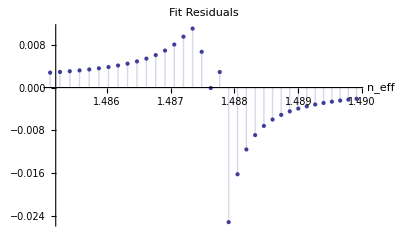

```mathematica
thefit⟦3⟧
```

```mathematica
NotebookSave[]
```

### Example 1

```mathematica
λ=1.0;
n1=1.503;
n2=1.5;
width=4.0; 
d2=1.3;
Nt=701; 
indxlist={{0.0,n1},{d2,n2},{width,n1},{0.0,n2}};
```

```mathematica
data=ScatteringMatrixAnalysis[Nt,λ,True,indxlist];
```

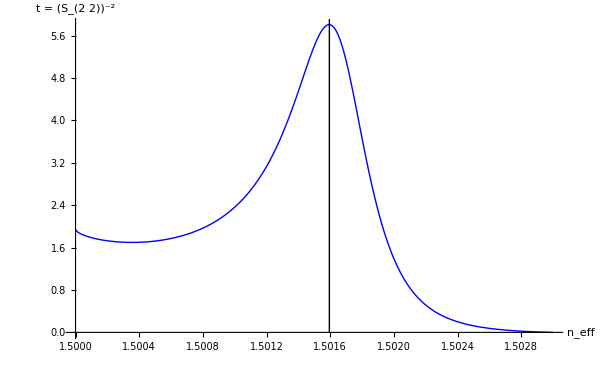

```mathematica
pltdata4=Map[{#1⟦1⟧,Abs[1.0/(#1⟦5⟧)^2]}&,data];
plt4=ListPlot[pltdata4,Joined->True,PlotRange->{All,All},PlotMarkers->None,AxesLabel->{"n_eff","t = (S_(2 2))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Blue},{Thick,Dashed,Red},Dotted},ImageSize->{600,360},Epilog->Line[{{1.501594415,0},{1.501594415,+10}}]]
```

```mathematica
xl=1.501;xu=1.502;
datasubset=Select[pltdata4,#1⟦1⟧>xl&&#1⟦1⟧<xu&];
```

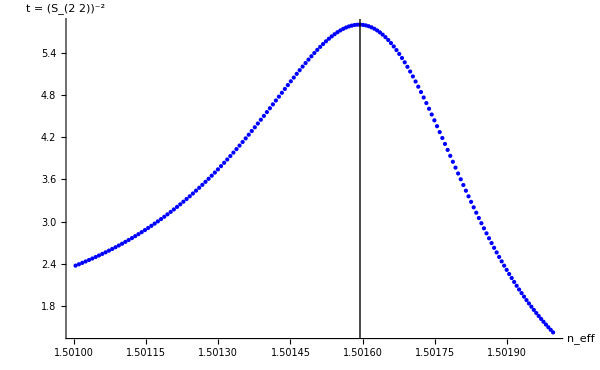

```mathematica
ListPlot[datasubset,Joined->False,PlotRange->{All,All},PlotMarkers->None,AxesLabel->{"n_eff","t = (S_(2 2))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Blue},{Thick,Dashed,Red},Dotted},ImageSize->{600,360},Epilog->{Line[{{1.501594415,0},{1.501594415,+10}}]}]
```

```mathematica
aa=6.0;
bb=1.5016; 
gg=1×10^-3;
thefit=LorentzFit[datasubset,aa,bb,gg];
```

The peak is located at 1.50154

The full-width at half-max is 0.00034736

The peak value is 5.70547

The R^2 parameter for the fit is 0.991671

The Adjusted R^2 parameter for the fit is 0.991519

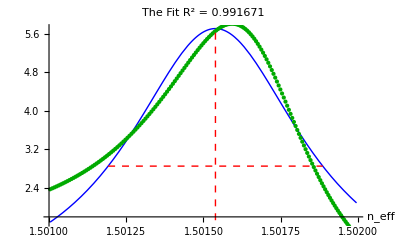

```mathematica
thefit⟦2⟧
```

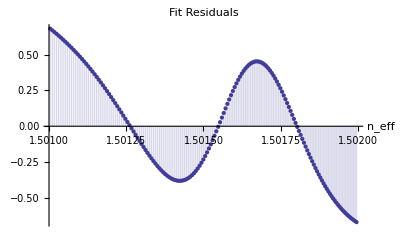

```mathematica
thefit⟦3⟧
```

```mathematica
NotebookSave[]
```

### Example 2

```mathematica
λ=1.0;
n1=3.38;
n2=3.17;
width=2.0; 
d2=0.5;
Nt=501; 
indxlist={{0.0,n1},{d2,n2},{width,n1},{0.0,n2}};
```

```mathematica
data=ScatteringMatrixAnalysis[Nt,λ,True,indxlist];
```

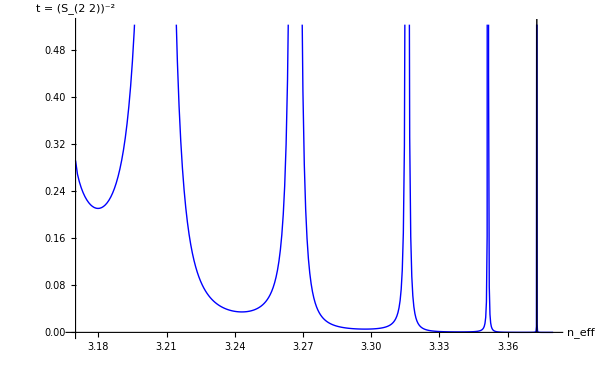

```mathematica
pltdata4=Map[{#1⟦1⟧,Abs[1.0/(#1⟦5⟧)^2]}&,data];
plt4=ListPlot[pltdata4,Joined->True,PlotRange->{All,Automatic},PlotMarkers->None,AxesLabel->{"n_eff","t = (S_(2 2))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Blue},{Thick,Dashed,Red},Dotted},ImageSize->{600,360},Epilog->Line[{{3.372834506,0},{3.372834506,+10}}]]
```

```mathematica
xl=3.37;xu=3.375;
datasubset=Select[pltdata4,#1⟦1⟧>xl&&#1⟦1⟧<xu&];
```

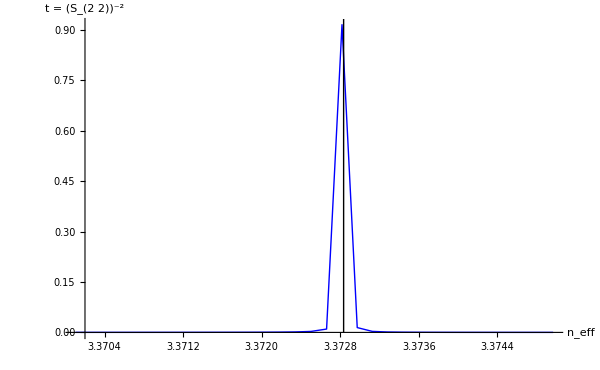

```mathematica
ListPlot[datasubset,Joined->True,PlotRange->{All,All},PlotMarkers->None,AxesLabel->{"n_eff","t = (S_(2 2))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Blue},{Thick,Dashed,Red},Dotted},ImageSize->{600,360},Epilog->{Line[{{3.372834506,0},{3.372834506,+10}}]}]
```

```mathematica
aa=0.3;
bb=3.373; 
gg=1×10^-5;
thefit=LorentzFit[datasubset,aa,bb,gg];
```

The peak is located at 3.37283

The full-width at half-max is 0.0000119617

The peak value is 2.03219

The R^2 parameter for the fit is 1.

The Adjusted R^2 parameter for the fit is 0.999999

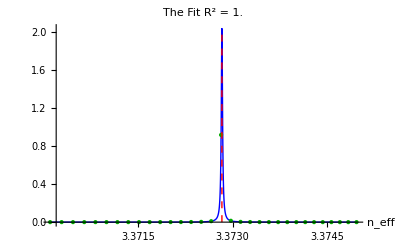

```mathematica
thefit⟦2⟧
```

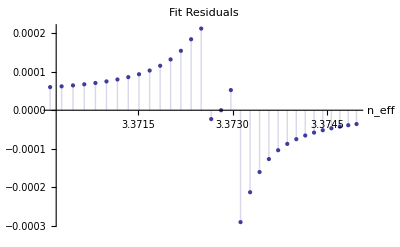

```mathematica
thefit⟦3⟧
```

```mathematica
NotebookSave[]
```

### Example 3

```mathematica
λ=1.55;
n1=3.38;
n2=3.17;
width=2.0; 
d2=0.5;
Nt=501; 
indxlist={{0.0,n1},{d2,n2},{width,n1},{0.0,n2}};
```

```mathematica
data=ScatteringMatrixAnalysis[Nt,λ,True,indxlist];
```

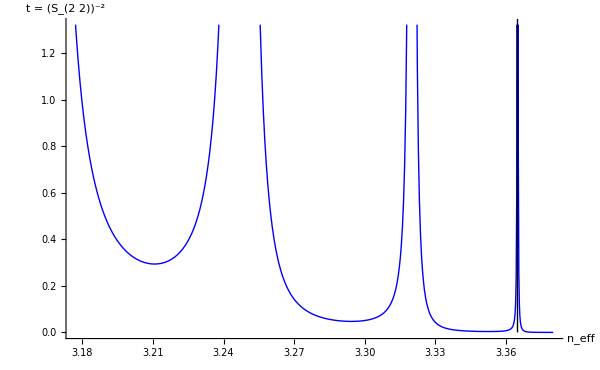

```mathematica
pltdata4=Map[{#1⟦1⟧,Abs[1.0/(#1⟦5⟧)^2]}&,data];
plt4=ListPlot[pltdata4,Joined->True,PlotRange->{All,Automatic},PlotMarkers->None,AxesLabel->{"n_eff","t = (S_(2 2))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Blue},{Thick,Dashed,Red},Dotted},ImageSize->{600,360},Epilog->Line[{{3.364870463,0},{3.364870463,+10}}]]
```

```mathematica
xl=3.36;xu=3.37;
datasubset=Select[pltdata4,#1⟦1⟧>xl&&#1⟦1⟧<xu&];
```

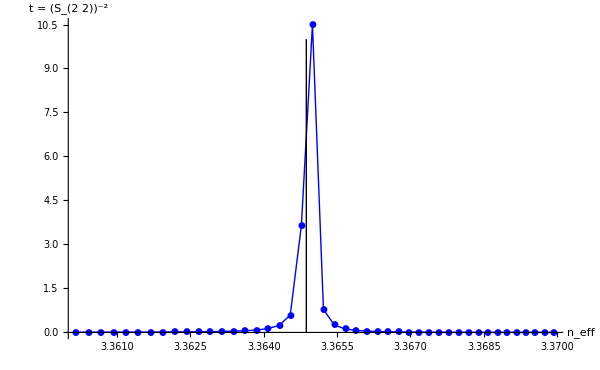

```mathematica
ListPlot[datasubset,Joined->True,PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"n_eff","t = (S_(2 2))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Blue},{Thick,Dashed,Red},Dotted},ImageSize->{600,360},Epilog->{Line[{{3.364870463,0},{3.364870463,+10}}]}]
```

```mathematica
aa=10;
bb=3.364; 
gg=1×10^-3;
thefit=LorentzFit[datasubset,aa,bb,gg];
```

The peak is located at 3.36491

The full-width at half-max is 0.0000194354

The peak value is 202.198

The R^2 parameter for the fit is 0.999961

The Adjusted R^2 parameter for the fit is 0.999958

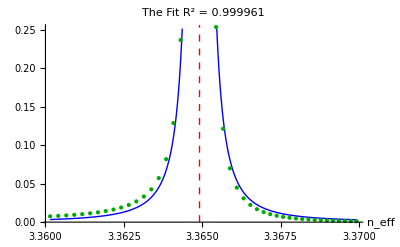

```mathematica
thefit⟦2⟧
```

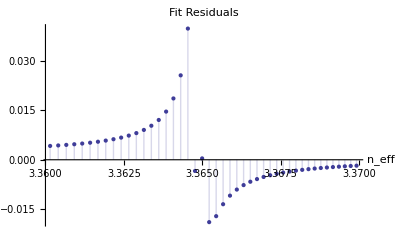

```mathematica
thefit⟦3⟧
```

```mathematica
NotebookSave[]
```

### Example 4 Waveguide Bend

```mathematica
λ=1.55;
n1=3.219;
n2=3.17;
width=1.0; 
d2=1.0;
Nt=501; 
(*indxlist={{0.0,n1},{d2,n2},{width,n1},{0.0,n2}};*)
```

```mathematica
rindx[x_]:=Which[
Abs[x]≤0.5width,n1,
Abs[x]>0.5width,n2
]
```

```mathematica
R=1000.0;
```

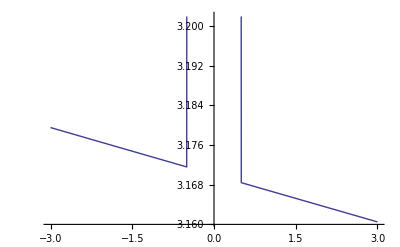

```mathematica
Plot[ⅇ^(-x/R)rindx[x],{x,-3,3}]
```

```mathematica
xl=-3.0; xu=3.0; 
nstps=31;
indxdata=Table[0,{0}];
indxdataalt=Table[0,{0}];
AppendTo[indxdata,{0.0,ⅇ^((0.5width)/R)n1}];
AppendTo[indxdataalt,{xl,ⅇ^((0.5width)/R)n1}];
dx=N[(xu-xl)/(nstps-1)];
x=xl;
Do[
AppendTo[indxdata,{dx,ⅇ^(-x/R)rindx[x]}];
AppendTo[indxdataalt,{x,ⅇ^(-x/R)rindx[x]}];
x=x+dx; 
,{i,1,nstps}];
AppendTo[indxdata,{0.0,ⅇ^(-x/R)rindx[x]}];
```

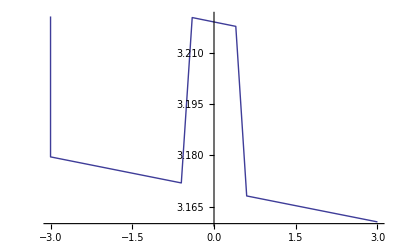

```mathematica
ListPlot[indxdataalt,Joined->True,PlotRange->{All,All}]
```

```mathematica
data=ScatteringMatrixAnalysis[Nt,λ,True,indxdata];
```

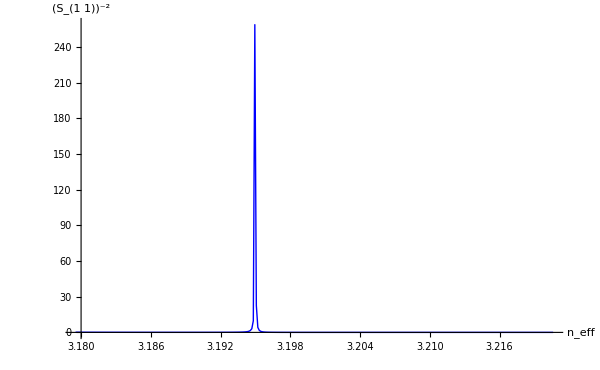

```mathematica
pltdata1=Map[{#1⟦1⟧,Abs[1.0/(#1⟦2⟧)^2]}&,data]; 
plt1=ListPlot[pltdata1,Joined->True,PlotRange->{All,All},AxesLabel->{"n_eff","(S_(1 1))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{Thick,Blue},ImageSize->{600,360}]
```

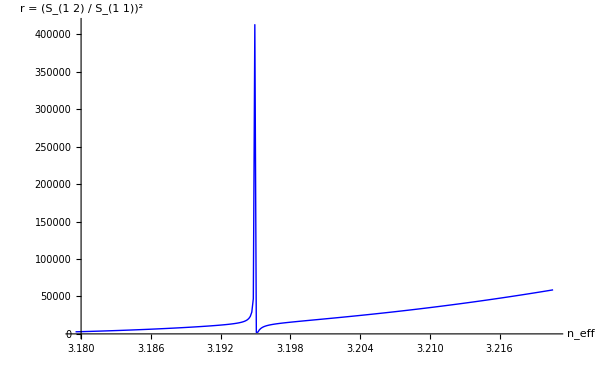

```mathematica
pltdata2=Map[{#1⟦1⟧,Abs[(#1⟦3⟧)^2/(#1⟦2⟧)^2]}&,data];
plt2=ListPlot[pltdata2,Joined->True,PlotRange->{All,All},AxesLabel->{"n_eff","r = (S_(1 2) / S_(1 1))^2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{Thick,Blue},ImageSize->{600,360}]
```

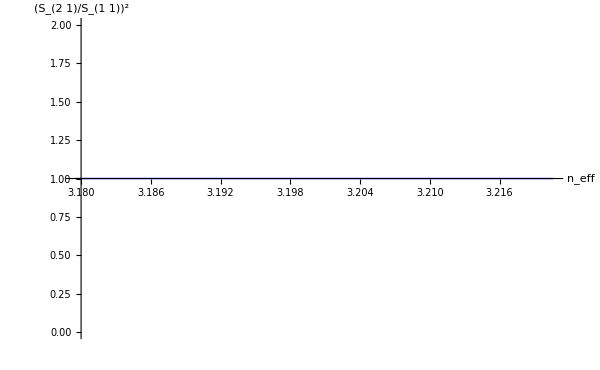

```mathematica
pltdata3=Map[{#1⟦1⟧,Abs[(#1⟦4⟧)^2/(#1⟦2⟧)^2]}&,data];
plt3=ListPlot[pltdata3,Joined->True,PlotRange->{All,All},AxesLabel->{"n_eff","(S_(2 1)/S_(1 1))^2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{Thick,Blue},ImageSize->{600,360}
]
(*Show[plt3,lines]*)
```

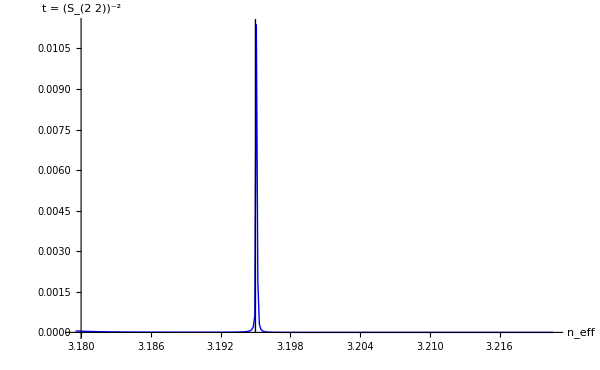

```mathematica
pltdata4=Map[{#1⟦1⟧,Abs[1.0/(#1⟦5⟧)^2]}&,data];
plt4=ListPlot[pltdata4,Joined->True,PlotRange->{All,All},PlotMarkers->None,AxesLabel->{"n_eff","t = (S_(2 2))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Blue},{Thick,Dashed,Red},Dotted},ImageSize->{600,360},Epilog->Line[{{3.195,0},{3.195,+50}}]]
```

```mathematica
xl=3.192;xu=3.196;
datasubset=Select[pltdata4,#1⟦1⟧>xl&&#1⟦1⟧<xu&];
```

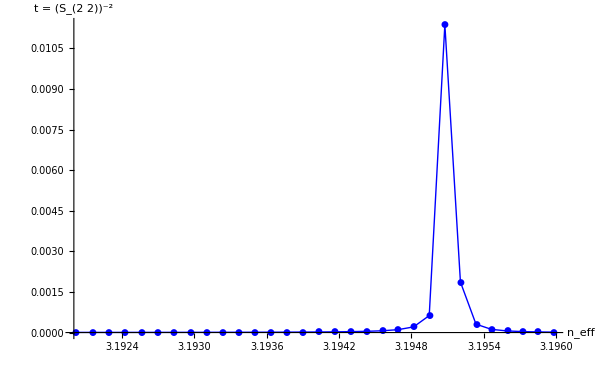

```mathematica
ListPlot[datasubset,Joined->True,PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"n_eff","t = (S_(2 2))^-2"},AxesStyle->Thick,LabelStyle->{Bold,18},PlotStyle->{{Thick,Blue},{Thick,Dashed,Red},Dotted},ImageSize->{600,360},Epilog->{Line[{{3.1965,0},{3.1965,+50}}]}]
```

```mathematica
aa=0.02;
bb=3.194; 
gg=1×10^-3;
thefit=LorentzFit[datasubset,aa,bb,gg];
```

The peak is located at 3.19511

The full-width at half-max is 0.0000161595

The peak value is 0.0650871

The R^2 parameter for the fit is 0.99998

The Adjusted R^2 parameter for the fit is 0.999977

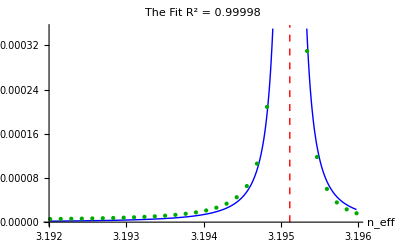

```mathematica
thefit⟦2⟧
```

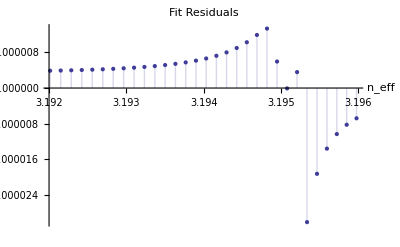

```mathematica
thefit⟦3⟧
```

```mathematica
NotebookSave[]
```